Funzioni ricorsive

```mathematica
f[n_;(*n ∈ℕ*)]:=n f[n-1.0]
```

```mathematica
f[0.0]:=1.0
```

```mathematica
f[10.1]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of f[-1011.9-1].

Hold[10.1 f[10.1-1]]

```mathematica
Table[f[k],{k,0,10}]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
10
```

```mathematica
n ∈ℂ
```

n∈ℂ

```mathematica
fib[0]=0
fib[1]=1
fib[n_]:=fib[n-1]+fib[n-2]
```

0

1

```mathematica
a=Table[fib[k],{k,0,10}]
```

{0,1,1,2,3,5,8,13,21,34,55}

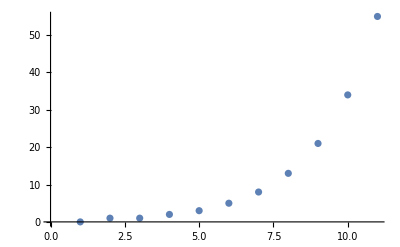

```mathematica
ListPlot[a]
```

```mathematica
a[[3;;10]]
```

{1,2,3,5,8,13,21,34}

```mathematica
Table[Prime[k],{k,100,200}]
```

{541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223}

```mathematica
b=BaseForm[1217 1223,2]
c=IntegerDigits[1217 1223,31]
```

101101011011000000111_2

{1,18,29,24,19}

```mathematica
c[[4]]
```

0

```mathematica
BitXor[61,2]
```

63

```mathematica
BaseForm[61,56]
BaseForm[15,2]
```

BaseForm::basf: Requested base 56 should be an integer between 2 and 36.

BaseForm[61,56]

1111_2

```mathematica
BaseForm[50,2]
```

110010_2

```mathematica
Poln[a_,x_]:=
```

```mathematica
coeff={1,18,29,24,19}
var={x^4,x^3,x^2,x,1}
coeff var
```

{1,18,29,24,19}

{x^4,x^3,x^2,x,1}

{x^4,18 x^3,29 x^2,24 x,19}

```mathematica
lax:=Total[coeff var]
```

```mathematica
Pol[x_]:=lax
```

```mathematica
N[Solve[lax==0,{x}]]
```

{{x→-0.194301-0.925113 ⅈ},{x→-0.194301+0.925113 ⅈ},{x→-16.3075},{x→-1.30385}}

```mathematica
a
```

{0,1,1,2,3,5,8,13,21,34,55}

```mathematica
Pol[-1.30385]
```

19+24 x+29 x^2+18 x^3+x^4

```mathematica
Poln[a_,x_]:=Total[Table[a[[k]]x^(k-1),{k,1,Length[a]}]]
```

```mathematica
Poln[coeff,x]
```

1+18 x+29 x^2+24 x^3+19 x^4

```mathematica
Solve[Poln[coeff==0,x],{x}]
```

Solve::naqs: 1&&18&&29&&24&&19 is not a quantified system of equations and inequalities.

Solve[{1,18,29,24,19},{x}]